## t vs C Plot for b=1.769

The data to import “CT3.txt”comes from the notebook “Fourier Coefficients for Fig2.nb”.
The txt file and the notebook can be found in the same folder.

### Data Import: (*change it to the local directory where the CT3.txt file is*)

```mathematica
directorio="(*your directory here*)\\";
```

#### We import the data:

```mathematica
cT3(*n,t, fourier coefficients from 12 to 18 *)=Import[StringJoin[directorio,"cT3.txt"],"TSV"];
cT3=ToExpression[cT3];
```

```mathematica
mx3=Table[Position[cT3⟦i,t⟧,Max[Abs[cT3⟦i,t⟧]]]⟦1,1⟧,{i,1,Dimensions[cT3]⟦1⟧},{t,1,Dimensions[cT3]⟦2⟧}];
```

```mathematica
gra3(*n, maximum coefficient value at time t*)=Table[cT3⟦i,t,mx3⟦i,t⟧⟧,{i,1,Length[cT3]},{t,1,Dimensions[cT3]⟦2⟧}];
```

#### And define the time step (to adjust the scale):

```mathematica
tn3=Table[i+0.1,{i,0,50*0.64468*30,50*0.64468}];
list=Table[Transpose[{tn3,gra3⟦i⟧}],{i,1,Length[gra3]}];
```

### Plots:

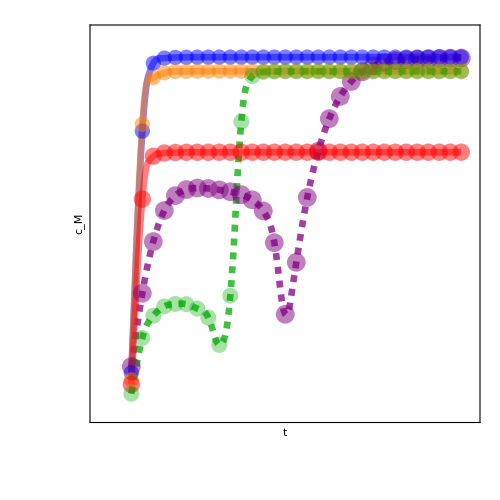

```mathematica
C3s=ListPlot[list,PlotRange->{{-99,1000},{0.1,.275}},Joined->True,AspectRatio->1, Frame->True,FrameTicks->{{None,{0.1,.15,.2,.25}},{None,{0,250,500,750,1000}}}, ImageSize->500, FrameTicksStyle->Directive[Gray,28], FrameLabel->{Text[Style["t",38,Italic, Black]],Text[Style["c_M",38,Italic, Black]]},PlotStyle->{{Opacity[0.75,Purple],Dashed,Thickness[0.0095]},{Opacity[0.5,Blue],Thickness[0.0095]},{Opacity[0.5,Orange],Thickness[0.0095]},{Opacity[0.5,Red],Thickness[0.0095]},{Opacity[0.75,Darker[Green]],Dashed,Thickness[0.0095]}},InterpolationOrder->2,Epilog->{{PointSize[0.027],Opacity[0.5,Purple],Point[list[[1]]]},{PointSize[0.022],Opacity[0.5,Blue],Point[list[[2]]]},{PointSize[0.022],Opacity[0.5,Orange],Point[list[[3]]]},{PointSize[0.025],Opacity[0.5,Red],Point[list[[4]]]},{PointSize[0.023],Opacity[0.35,Darker[Green]],Point[list[[5]]]}}]
```

```mathematica
Export["figura2a.png",C3s,ImageResolution->250]
```

figura2a.png